```mathematica
fromlinear[x_] := Piecewise[{{12.92 x, x ≤ 0.0031308}}, 1.055 x^(1/2.4)-0.055]
```

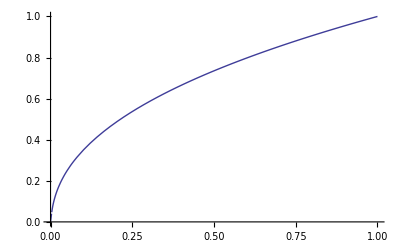

```mathematica
Plot[fromlinear[x], {x,0,1}]
```

```mathematica
getlinear[i_, n_] := Table[{x,fromlinear[x]}, {x, i/n, (i+1)/n, .00025}]
```

```mathematica
Table[Fit[getlinear[i,128], {1, x}, x] , {i, 0, 128-1}]
```

```mathematica
fromsrgb[x_] := Piecewise[{{x/12.92, x ≤ .04045}}, ((x + 0.055) / 1.055)^2.4]
```

```mathematica
getsrgb[i_, n_] := Table[{x,fromsrgb[x]}, {x, i/n, (i+1)/n, .00025}]
```

```mathematica
Table[Fit[getsrgb[i,256], {1, x}, x] , {i, 0, 256-1}]
```

{-8.13152×10^-20+0.0773994 x,5.42101×10^-20+0.0773994 x,8.13152×10^-19+0.0773994 x,4.33681×10^-19+0.0773994 x,-2.1684×10^-19+0.0773994 x,2.27682×10^-18+0.0773994 x,-1.0842×10^-18+0.0773994 x,2.1684×10^-19+0.0773994 x,-1.0842×10^-17+0.0773994 x,1.17094×10^-17+0.0773994 x,-0.00006639+0.0790642 x,-0.00027113+0.0838425 x,-0.000487716+0.0884703 x,-0.00072594+0.0931684 x,-0.000986268+0.0979352 x,-0.00126915+0.102769 x,-0.00157503+0.107669 x,-0.00190432+0.112633 x,-0.00225746+0.117661 x,-0.00263485+0.122751 x,-0.00303688+0.127902 x,-0.00346395+0.133113 x,-0.00391644+0.138383 x,-0.00439471+0.143711 x,-0.00489914+0.149096 x,-0.00543009+0.154537 x,-0.0059879+0.160033 x,-0.00657292+0.165584 x,-0.0071855+0.171189 x,-0.00782596+0.176846 x,-0.00849463+0.182556 x,-0.00919183+0.188317 x,-0.00991789+0.194129 x,-0.0106731+0.199991 x,-0.0114578+0.205903 x,-0.0122723+0.211863 x,-0.0131168+0.217872 x,-0.0139917+0.223929 x,-0.0148973+0.230032 x,-0.0158338+0.236183 x,-0.0168015+0.242379 x,-0.0178007+0.248621 x,-0.0188317+0.254909 x,-0.0198948+0.26124 x,-0.0209902+0.267616 x,-0.0221181+0.274036 x,-0.023279+0.280499 x,-0.0244729+0.287005 x,-0.0257002+0.293553 x,-0.0269611+0.300143 x,-0.0282558+0.306775 x,-0.0295847+0.313448 x,-0.0309479+0.320162 x,-0.0323458+0.326916 x,-0.0337785+0.33371 x,-0.0352462+0.340545 x,-0.0367493+0.347418 x,-0.0382879+0.354331 x,-0.0398623+0.361282 x,-0.0414727+0.368272 x,-0.0431193+0.3753 x,-0.0448024+0.382366 x,-0.0465222+0.389469 x,-0.0482789+0.39661 x,-0.0500727+0.403787 x,-0.0519038+0.411001 x,-0.0537725+0.418252 x,-0.055679+0.425538 x,-0.0576234+0.43286 x,-0.059606+0.440218 x,-0.061627+0.447611 x,-0.0636867+0.45504 x,-0.0657851+0.462503 x,-0.0679225+0.47 x,-0.0700991+0.477532 x,-0.0723151+0.485098 x,-0.0745708+0.492698 x,-0.0768662+0.500332 x,-0.0792017+0.507999 x,-0.0815773+0.515699 x,-0.0839933+0.523432 x,-0.0864499+0.531198 x,-0.0889473+0.538997 x,-0.0914856+0.546828 x,-0.0940651+0.554691 x,-0.0966859+0.562586 x,-0.0993482+0.570513 x,-0.102052+0.578471 x,-0.104798+0.586461 x,-0.107586+0.594482 x,-0.110416+0.602534 x,-0.113289+0.610617 x,-0.116204+0.618731 x,-0.119162+0.626875 x,-0.122163+0.63505 x,-0.125207+0.643254 x,-0.128295+0.651489 x,-0.131425+0.659754 x,-0.1346+0.668048 x,-0.137818+0.676372 x,-0.141081+0.684725 x,-0.144387+0.693107 x,-0.147738+0.701519 x,-0.151133+0.709959 x,-0.154573+0.718428 x,-0.158058+0.726926 x,-0.161587+0.735452 x,-0.165162+0.744007 x,-0.168783+0.752589 x,-0.172448+0.7612 x,-0.176159+0.769839 x,-0.179917+0.778505 x,-0.18372+0.7872 x,-0.187569+0.795921 x,-0.191464+0.80467 x,-0.195406+0.813447 x,-0.199394+0.82225 x,-0.203429+0.831081 x,-0.207511+0.839938 x,-0.211641+0.848822 x,-0.215817+0.857733 x,-0.22004+0.86667 x,-0.224311+0.875634 x,-0.22863+0.884624 x,-0.232997+0.89364 x,-0.237411+0.902683 x,-0.241874+0.911751 x,-0.246385+0.920845 x,-0.250944+0.929965 x,-0.255551+0.93911 x,-0.260208+0.948281 x,-0.264913+0.957477 x,-0.269667+0.966699 x,-0.274471+0.975946 x,-0.279323+0.985218 x,-0.284225+0.994515 x,-0.289177+1.00384 x,-0.294178+1.01318 x,-0.299229+1.02255 x,-0.30433+1.03195 x,-0.309481+1.04137 x,-0.314682+1.05082 x,-0.319934+1.06029 x,-0.325236+1.06978 x,-0.330589+1.0793 x,-0.335993+1.08884 x,-0.341448+1.0984 x,-0.346953+1.10799 x,-0.35251+1.11761 x,-0.358118+1.12724 x,-0.363778+1.1369 x,-0.369489+1.14659 x,-0.375252+1.15629 x,-0.381067+1.16603 x,-0.386934+1.17578 x,-0.392853+1.18556 x,-0.398824+1.19536 x,-0.404848+1.20518 x,-0.410924+1.21503 x,-0.417053+1.2249 x,-0.423235+1.23479 x,-0.429469+1.2447 x,-0.435757+1.25464 x,-0.442098+1.2646 x,-0.448492+1.27458 x,-0.454939+1.28459 x,-0.46144+1.29461 x,-0.467995+1.30466 x,-0.474603+1.31473 x,-0.481266+1.32483 x,-0.487982+1.33494 x,-0.494753+1.34508 x,-0.501578+1.35524 x,-0.508457+1.36542 x,-0.515391+1.37562 x,-0.522379+1.38585 x,-0.529423+1.39609 x,-0.536521+1.40636 x,-0.543674+1.41665 x,-0.550883+1.42696 x,-0.558146+1.43729 x,-0.565465+1.44764 x,-0.57284+1.45802 x,-0.58027+1.46841 x,-0.587756+1.47883 x,-0.595298+1.48927 x,-0.602896+1.49972 x,-0.61055+1.5102 x,-0.61826+1.5207 x,-0.626026+1.53122 x,-0.633849+1.54177 x,-0.641728+1.55233 x,-0.649665+1.56291 x,-0.657658+1.57351 x,-0.665708+1.58414 x,-0.673814+1.59478 x,-0.681979+1.60545 x,-0.6902+1.61613 x,-0.698479+1.62684 x,-0.706815+1.63756 x,-0.715209+1.64831 x,-0.72366+1.65907 x,-0.732169+1.66986 x,-0.740737+1.68066 x,-0.749362+1.69149 x,-0.758045+1.70233 x,-0.766787+1.7132 x,-0.775587+1.72408 x,-0.784446+1.73498 x,-0.793363+1.74591 x,-0.802339+1.75685 x,-0.811374+1.76781 x,-0.820468+1.7788 x,-0.829621+1.7898 x,-0.838832+1.80082 x,-0.848104+1.81186 x,-0.857434+1.82292 x,-0.866824+1.834 x,-0.876274+1.84509 x,-0.885783+1.85621 x,-0.895352+1.86735 x,-0.904981+1.8785 x,-0.91467+1.88968 x,-0.924419+1.90087 x,-0.934229+1.91208 x,-0.944099+1.92331 x,-0.954029+1.93456 x,-0.964019+1.94583 x,-0.974071+1.95712 x,-0.984183+1.96842 x,-0.994356+1.97974 x,-1.00459+1.99109 x,-1.01488+2.00245 x,-1.02524+2.01383 x,-1.03566+2.02522 x,-1.04614+2.03664 x,-1.05668+2.04808 x,-1.06728+2.05953 x,-1.07794+2.071 x,-1.08867+2.08249 x,-1.09945+2.094 x,-1.1103+2.10552 x,-1.12122+2.11706 x,-1.13219+2.12863 x,-1.14322+2.1402 x,-1.15432+2.1518 x,-1.16548+2.16342 x,-1.17671+2.17505 x,-1.18799+2.1867 x,-1.19934+2.19837 x,-1.21075+2.21006 x,-1.22223+2.22176 x,-1.23376+2.23348 x,-1.24537+2.24522 x,-1.25703+2.25698 x,-1.26876+2.26875 x}